```mathematica
<<NFPackages`structuralMechanicsBook` // Quiet
```

```mathematica
shear[ {kb_, kt_}, {P_, Mb_, Mt_}, EI_, L_ ] := (12 (kb+kt+4 kb kt) P EI)/(L^2 (-3 (1+2 kt) Mb-3 (1+2 kb) Mt+(3+4 kb+4 kt+4 kb kt) L P))
```

```mathematica
mbmt[ {kb_, kt_}, {P_, Mb_, Mt_}, L_ ] := {-(kt Mb)/(kb+kt+4 kb kt)+(kb Mt)/(kb+kt+4 kb kt)-(kb (1+2 kt) L P)/(kb+kt+4 kb kt),-(kt Mb)/(kb+kt+4 kb kt)+(kb Mt)/(kb+kt+4 kb kt)+((1+2 kb) kt L P)/(kb+kt+4 kb kt)}
```

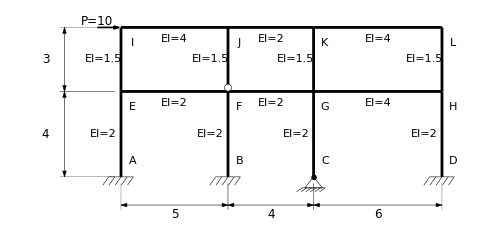

"Approximate analysis of a side loaded building" |  |  |  | 
"Preliminary calculations" |  |  |  | 
"Floor = 1" |  |  |  | 
"column" | 1 | 2 | 3 | 4
"stiffness factor at top" | "1.200" | "2.700" | "3.500" | "2.000"
"stiffness factor at bottom" | ∞ | ∞ | 0 | ∞
"Floor = 2" |  |  |  | 
"column" | 1 | 2 | 3 | 4
"stiffness factor at top" | "2.400" | "3.900" | "3.500" | "2.000"
"stiffness factor at bottom" | "1.200" | 0 | "3.500" | "2.000"

```mathematica
(12 (kb+kt+4 kb kt) P EI)/(L^2 (+3 (1+2 kt) Mb+3 (1+2 kb) Mt+(3+4 kb+4 kt+4 kb kt) L P)) /. 
{kb -> 3.5, 
kt -> 3.5, 
P -> 3.493, Mb -> 3.414, Mt -> 0, 
EI -> 1.5, L -> 3 }
```

0.425116

"Iteration number = 2" |  |  |  |  | 
"Floor = 1" |  |  |  |  | 
"column number" | 1 | 2 | 3 | 4 | ""
"shear stiffness" | "0.202" | "0.299" | "0.061" | "0.240" | "0.802"
"relative shear stiffness" | "0.252" | "0.373" | "0.076" | "0.299" | 1
"shear" | "2.518" | "3.730" | "0.758" | "2.994" | 10
"Internal moment at top" | "3.546" | "6.828" | "3.032" | "4.848" | ""
"Internal moment at bottom" | "-6.525" | "-8.093" | 0 | "-7.129" | ""
"Floor = 2" |  |  |  |  | 
"column number" | 1 | 2 | 3 | 4 | ""
"shear stiffness" | "0.259" | "0.140" | "0.425" | "0.298" | "1.122"
"relative shear stiffness" | "0.231" | "0.125" | "0.379" | "0.266" | 1
"shear" | "2.305" | "1.246" | "3.789" | "2.659" | 10
"Internal moment at top" | "4.450" | "3.738" | "5.897" | "4.542" | ""
"Internal moment at bottom" | "-2.466" | 0 | "-5.471" | "-3.436" | ""

"Iteration number = 1" |  |  |  |  | 
"Floor = 1" |  |  |  |  | 
"column number" | 1 | 2 | 3 | 4 | ""
"shear stiffness" | "0.247" | "0.299" | "0.077" | "0.281" | "0.905"
"relative shear stiffness" | "0.273" | "0.331" | "0.085" | "0.311" | 1
"shear" | "2.732" | "3.305" | "0.853" | "3.109" | 10
"Internal moment at top" | "4.522" | "6.050" | "3.414" | "5.527" | ""
"Internal moment at bottom" | "-6.407" | "-7.171" | 0 | "-6.909" | ""
"Floor = 2" |  |  |  |  | 
"column number" | 1 | 2 | 3 | 4 | ""
"shear stiffness" | "0.349" | "0.140" | "0.467" | "0.381" | "1.336"
"relative shear stiffness" | "0.261" | "0.105" | "0.349" | "0.285" | 1
"shear" | "2.609" | "1.046" | "3.493" | "2.852" | 10
"Internal moment at top" | "4.224" | "3.139" | "5.240" | "4.277" | ""
"Internal moment at bottom" | "-3.603" | 0 | "-5.240" | "-4.277" | ""